```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Mass m, kinetic energy ϵ incident on a target M

```mathematica
Solve[ReplaceAll[(γ-1)m==ϵ,γ->1/Sqrt[1-β^2]],β]
```

{{β→-(√ϵ √(2 m+ϵ))/(m+ϵ)},{β→(√ϵ √(2 m+ϵ))/(m+ϵ)}}

#### Rutherford cross section to loss energy Ed (Classical and Mott scattering spin correction)

```mathematica
rutherford=(2Pi α^2 Z^2)/(M β^2 Ed^2);
rutherford0=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin);
```

#### Pauli-Blocked number density (assuming relativistic Fermi gas)

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
ReplaceAll[npaulirel,Ed->Ef]
```

Ef^3/(3 π^2)

```mathematica
Convert[10^33 Centimeter^-3(200 Mega ElectronVolt Fermi)^3,(Mega ElectronVolt)^3]
```

8 ElectronVolt^3 Mega^3

```mathematica
(3 Pi^2 n)^(1/3)/.n->8//N
```

6.18734

```mathematica
plotrel=Plot[ReplaceAll[npaulirel,{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];naiveplot=Plot[ReplaceAll[n*(Ed/Ef),{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];
```

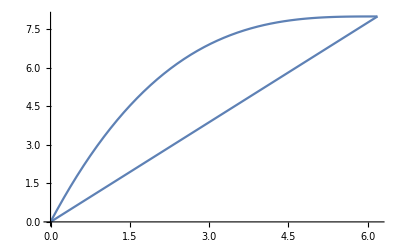

```mathematica
Show[plotrel,naiveplot]
```

#### Coulomb Log Parameters

```mathematica
collision[b_]:=(2 Z^2 α^2)/(M b^2 β^2)
Ekin=(2M β^2 γ^2)/(1+2γ (M/m)+(M/m)^2);
Ekinelectron=Ekin/2/.{M->0.511,m->0.511};
λTF=((6Pi α n)/Ef)^(-1/2);
Esc=collision[λTF];
Elattice:=(Z^2 α)/(n/Z)^(-1/3);
```

```mathematica
Esc/.{Z->1,α->1/137,M->10^4,Ef->(3 Pi^2 n)^(1/3)}/.{β->1,n->8}//N
```

1.89564×10^-9

```mathematica
Elattice/.{Z->6,α->1/137,M->10^4,Ef->(3 Pi^2 n)^(1/3)}/.{n->8}//N
```

0.28922

#### Stopping powers in all cases

```mathematica
Integrate[rutherford*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]
```

(2 n π Z^2 α^2 Log[emax/emin])/(M β^2)

```mathematica
SP=(2n π Z^2 α^2 Log[(emax/emin)])/(M β^2);
SP0=Integrate[rutherford0*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]/.ekin->Ekin;
SPpauli=Integrate[rutherford0*npaulirel*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]/.ekin->Ekin;
```

#### SP in units of MeV/(10^-5 cm)

```mathematica
Convert[(Mega ElectronVolt)^2 1/(200 Mega ElectronVolt*Fermi),(Mega ElectronVolt)/Centimeter]//N
```

(5.×10^10 ElectronVolt Mega)/Centimeter

#### Stopping power due to Coulomb Collisions off carbon nuclei - see emin, emax bounds

```mathematica
dedx:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP,{emin->Max[Esc,Elattice],emax->Ekin}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
electron=LogLogPlot[Evaluate[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->0.511]],{ϵ,10^-2,10^7},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
electronflat=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Thick,Blue}];
pion=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->140],{ϵ,10^-2,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick},PlotRange->All];
proton=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->8}],m->1000],{ϵ,10^-2,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
electron2=LogLogPlot[Evaluate[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.032}],m->0.511]],{ϵ,10^-2,10^7},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
electronflat2=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.032}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Thick,Blue}];
pion2=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.032}],m->140],{ϵ,10^-2,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
proton2=LogLogPlot[ReplaceAll[ReplaceAll[dedx 5.*^5,{α->1/137,M->12000,Z->6,n->0.032}],m->1000],{ϵ,10^-2,10^10},PlotLegends->{"Coulomb (nuclei)"},PlotStyle->{Blue,Thick}];
```

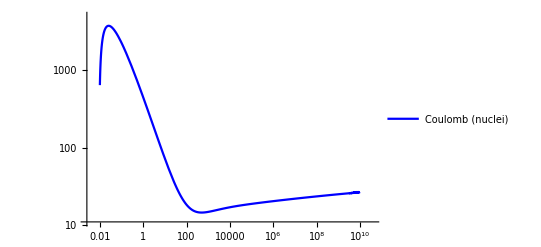

```mathematica
pion
```

#### Stopping power due to Coulomb Collisions off Electrons

```mathematica
dedxpaulideg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[SPpauli,{emin->Esc,emax->Min[Ekin,Ef]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
dedxpaulinondeg:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP0,emin->Min[Ef,Ekin]],emax->Ekin],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
dedxpaulidegelectron:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[SPpauli,{emin->Esc,emax->Min[Ekinelectron,Ef]}],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
dedxpaulidegfermi[ϵ_]:=If[ϵ>(3 Pi^2 n)^(1/3)/.n->8,dedxpaulidegelectron/.{α->1/137,M->0.511,Z->1,n->8}/.m->0.511,0];
dedxpaulidegfermi2[ϵ_]:=If[ϵ>(3 Pi^2 n)^(1/3)/.n->0.032,dedxpaulidegelectron/.{α->1/137,M->0.511,Z->1,n->0.032}/.m->0.511,0];
dedxpaulinondegelectron:=ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[ReplaceAll[1/Z SP0,emin->Min[Ef,Ekinelectron]],emax->Ekinelectron],Ef->(3 Pi^2 n)^(1/3)],γ->1/Sqrt[1-β^2]],β->(√ϵ √(2 m+ϵ))/(m+ϵ)];
```

```mathematica
electronpauli=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondegelectron+dedxpaulidegfermi[ϵ]) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->0.511],{ϵ,10^-1,10^7},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
electronpauliflat=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondegelectron+dedxpaulidegfermi[10^7]) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Orange,Thick}];
pionpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->140],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
protonpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->8}],m->1000],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
ionpauli=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->6,n->8}],m->12000],{ϵ,10,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Black,Thick}];
electronpauli2=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondegelectron+dedxpaulidegfermi2[ϵ]) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.032}],m->0.511],{ϵ,10^-1,10^7},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
electronpauliflat2=LogLogPlot[ReplaceAll[ReplaceAll[ (dedxpaulinondegelectron+dedxpaulidegfermi2[10^7]) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.032}],m->0.511]/.ϵ->10^7,{x,10^7,10^10},PlotStyle->{Orange,Thick}];
pionpauli2=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.032}],m->140],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
protonpauli2=LogLogPlot[ReplaceAll[ReplaceAll[(dedxpaulinondeg+dedxpaulideg) 5.*^5,{α->1/137,M->0.511,Z->1,n->0.032}],m->1000],{ϵ,10^-1,10^10},PlotLegends->{"Coulomb (electron)"},PlotStyle->{Orange,Thick}];
```

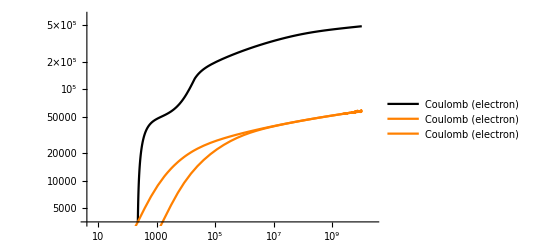

```mathematica
Show[ionpauli,protonpauli,pionpauli]
```

#### Examine the Coulomb Logarithm, find where scattering should “shut off” for protons and pions.

```mathematica
coulomblog={Max[Esc,Elattice],Ekin}/.{Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.{β->(√ϵ √(2 m+ϵ))/(m+ϵ)}/.{α->1/137,M->12000,Z->6,n->8};
```

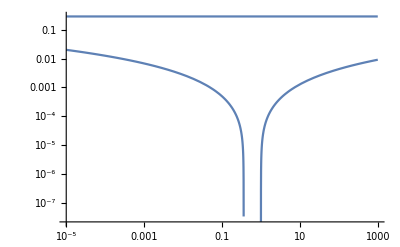

```mathematica
LogLogPlot[coulomblog/.m->0.511,{ϵ,0.00001,10^3}]
```

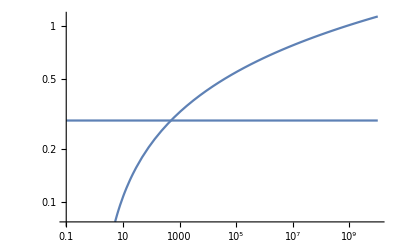

```mathematica
LogLogPlot[coulomblog/.m->140,{ϵ,0.1,10^10}]
```

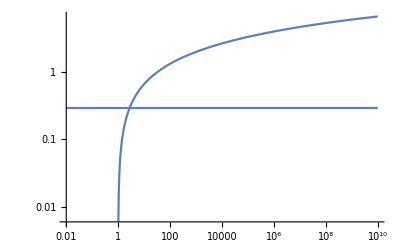

```mathematica
LogLogPlot[coulomblog/.m->1000,{ϵ,0.01,10^10}]
```

```mathematica
2Pi 8/6*6*(1/137)^2 1/0.1 0.5/12000 10 5*10^5//N
```

5.5794

```mathematica
2Pi 8/6*6*(1/137)^2 1/0.1^2 0.5/12000 10 10^2/12000 5*10^5//N
```

0.46495

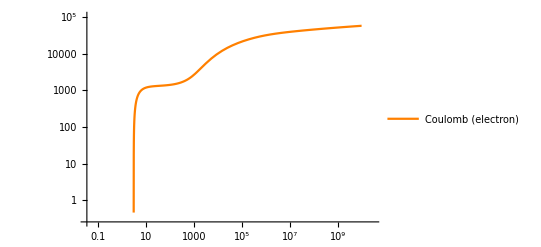

```mathematica
protonpauli
```

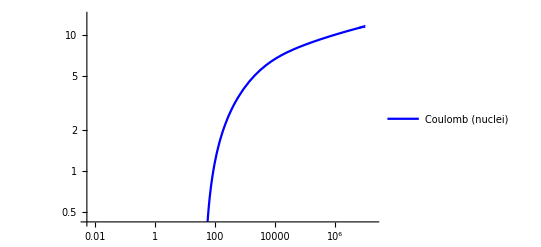

```mathematica
electron
```